# AMS-511 Foundations of Quantitative Finance

## Fall 2020 — Assignment 07

Robert J. Frey, Research Professor
Stony Brook University, Applied Mathematics and Statistics

Robert.Frey@StonyBrook.edu
http://www.ams.sunysb.edu/~frey

## Question 1.

Let r(t) denote the return of an asset in time period t, and assume that time varies over T periods, i.e., t=1,2, …,T-1, T. Let r_total denote the total return over the T periods. Note that the log return of rate r is computed by log[1+r]. Thus,

(1+r_total)=(1+r(1)) (1+r(2)) … (1+r(T-1)) (1+r(T))=∏_(t=1)^T (1+r(t))

Show that maximizing the log return of r(t) also maximizes r_total.

### Solution

Taking the log of both sides of the above we have

Log[1+r_total]=∑_(t=1)^T log[[1+r(t)]=T 𝔼[log(1+r(t)]]

Thus, maximizing the expected log return also maximizes the total log return. The log return is a monotonically increasing function of the return; hence, maximizing the total log return also maximizes the the total return.

## Question 2.

Consider a stock whose price at time t is S(t) and which has constant volatility σ= 18%. The risk free rate is r_f= 1%. Let S(0)=$102.25. Based on public information, the stock is involved in a lawsuit. If it wins the lawsuit its price will rise dramatically, and if it loses will fall dramatically. Your best estimate is that the lawsuit will be resolved in six months.

Using FinancialDerivative[ ] and vanilla European options, determine the price at t=0 of a suitable long straddle to take advantage of this situation.

Plot the value of the straddle at three months hence for values of the underlying from $75 to $125.

The lawsuit is settled early at three months and you close out the position. Plot the P&L graph for this strategy for values of the underlying from $75 to $125.

### Solution

#### Pricing the Straddle

The straddle is built from a long at-the-money put and call with an expiry at 6 months.

```mathematica
nInitialStraddlePrice=FinancialDerivative[{"European","Put"}, {"StrikePrice"-> 102.25, "Expiration"->0.5},  {"InterestRate"-> 0.01, "Volatility" -> 0.18, "CurrentPrice"-> 102.25}]+FinancialDerivative[{"European","Call"}, {"StrikePrice"-> 102.25, "Expiration"->0.5},  {"InterestRate"-> 0.01, "Volatility" -> 0.18, "CurrentPrice"-> 102.25}]
```

10.359

#### Price After Three Months

After the three months the straddle price as a function of the price of the underlying is

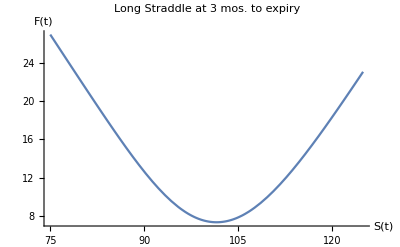

```mathematica
Plot[FinancialDerivative[{"European","Put"}, {"StrikePrice"-> 102.25, "Expiration"->0.25},  {"InterestRate"-> 0.01, "Volatility" -> 0.18, "CurrentPrice"-> s}]+FinancialDerivative[{"European","Call"}, {"StrikePrice"-> 102.25, "Expiration"->0.25},  {"InterestRate"-> 0.01, "Volatility" -> 0.18, "CurrentPrice"-> s}],{s,75,125},AxesOrigin->{70,0},PlotRange->All,PlotLabel->"Long Straddle at 3 mos. to expiry",AxesLabel->{"S(t)","F(t)"}]
```

#### Profit and Loss Assuming the Position is Closed at Three Months

If we close out the straddle after three months the profit and loss is the price realized by closing out the straddle minus the original cost of the straddle.

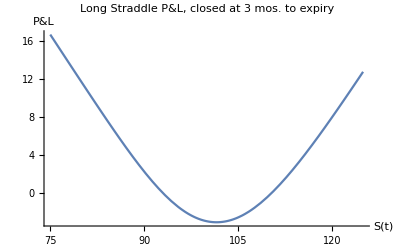

```mathematica
Plot[FinancialDerivative[{"European","Put"}, {"StrikePrice"-> 102.25, "Expiration"->0.25},  {"InterestRate"-> 0.01, "Volatility" -> 0.18, "CurrentPrice"-> s}]+FinancialDerivative[{"European","Call"}, {"StrikePrice"-> 102.25, "Expiration"->0.25},  {"InterestRate"-> 0.01, "Volatility" -> 0.18, "CurrentPrice"-> s}]-nInitialStraddlePrice,{s,75,125},AxesOrigin->{70,0},PlotRange->All,PlotLabel->"Long Straddle P&L, closed at 3 mos. to expiry",AxesLabel->{"S(t)","P&L"}]
```

## Question 3.

In the Notes for Lecture 07 we downloaded the daily price for the S&P 500 for 1960-01-01 to 2020-09-30 and then computed the daily log returns.

As in the Notes, use EstmatedDistribution[ ] to fit a NormalDistribution[ ] and a StudentTDistribution[ ] to the daily log returns.

Read the description for DistributionFitTest[ ] in the Documentation Center. Use it to evaluate how well each of the distributions above fit the data.

Read the description for ProbabilityPlot[ ] in the Documentation Center. Use it to evaluate how well each of the distributions above fit the data.

Using whichever of the two distributions are the most representative and assuming the daily log return is an i.i.d. random variable, what is the probability a given day’s log return is -10% or less?

Assuming there are 250 trading days in a year, how many years on average will there be between log return losses worse than -10%?

Using the raw data, what is the probability that a given day’s log return is -10% or less?

### Solution

#### Importing the Data

We can either repeat the download and computations of the Notes or Import[ ] the log returns we Export[ ]ed.

```mathematica
mxSP500LogReturn=Import[FileNameJoin[{NotebookDirectory[],"mxSP500LogReturn.m"}]];
```

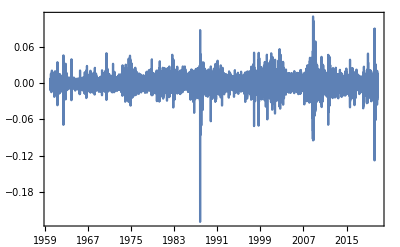

```mathematica
DateListPlot[mxSP500LogReturn,PlotRange->All]
```

#### Fitting the Distributions to the Log Returns

Fitting the distributions to the data.

```mathematica
distN=EstimatedDistribution[Last/@mxSP500LogReturn,NormalDistribution[m,s]]
```

NormalDistribution[0.000263406,0.0102886]

```mathematica
distT=EstimatedDistribution[Last/@mxSP500LogReturn,StudentTDistribution[m,s,d]]
```

StudentTDistribution[0.00046563,0.00621358,2.96381]

#### Hypothesis Tests

We can perform a quick hypothesis test using DistrbutionFitTest[ ] for the two distributions. Note that the null hypothesis that the data fits the subject distribution is rejected at a 95% confidence level, although the Student t distribution has a much higher p-value.

```mathematica
hypN=DistributionFitTest[Last/@mxSP500LogReturn,distN,"HypothesisTestData"];
```

```mathematica
hypN["PValueTable"]
```

| P-Value
Cramér-von Mises | 7.77156×10^-16

```mathematica
hypN["TestConclusion"]
```

The null hypothesis that the data is distributed according to the NormalDistribution[0.000263406,0.0102886] is rejected at the 5 percent level based on the Cramér-von Mises test.

```mathematica
hypT=DistributionFitTest[Last/@mxSP500LogReturn,distT,"HypothesisTestData"];
```

```mathematica
hypT["PValueTable"]
```

| P-Value
Cramér-von Mises | 0.0394155

```mathematica
hypT["TestConclusion"]
```

The null hypothesis that the data is distributed according to the StudentTDistribution[0.00046563,0.00621358,2.96381] is rejected at the 5 percent level based on the Cramér-von Mises test.

#### Probability Plots

We can see from the ProbabilityPlot[ ]s that the Student t, despite failing the hypothesis test, seems to fit the data quite well.

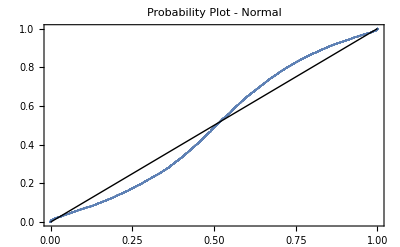

```mathematica
ProbabilityPlot[Last/@mxSP500LogReturn,distN,PlotLabel->"Probability Plot - Normal"]
```

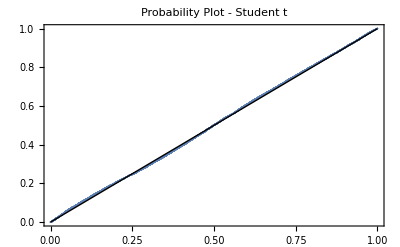

```mathematica
ProbabilityPlot[Last/@mxSP500LogReturn,distT,PlotLabel->"Probability Plot - Student t"]
```

## Question 4.

You are playing game at a casino. Your current wealth is w. Given your bet b (assuming 0≤b≤w), you have a 1/4 probability of winning back your original bet plus 3b and a 3/4 probability of losing the amount bet.

Use the Kelly criterion to determine your optimal bet size.

What is your expected wealth after one round of betting?

### Solution

Following the logic in the Notes we solve the following.

```mathematica
FullSimplify@Solve[D[(1/4 Log[w+3b]+3/4 Log[w-b]), b]==0,b]
```

{{b→0}}

The optimal bet is not to bet. The expected wealth after one round of betting is the original wealth w.